```mathematica
SetDirectory[NotebookDirectory[]];
PureBasis=Get[FileNameJoin[{Directory[],"files/basis.m"}]];
MUIJs=Get[FileNameJoin[{Directory[],"files/muijs.m"}]];
roots=Get[FileNameJoin[{Directory[],"files/roots.m"}]];
```

# Get Pure Int Variables

```mathematica
Variables[Cases[PureBasis,_Insertion,Infinity]/.Insertion[x___]:>x]//Sort
Topologies=Cases[(PureBasis/.Topology[x___]:>x),_List,Infinity];
HXBSUBTopos=Position[Topologies[[All,3]],0][[All,1]]
DBPureBasis=PureBasis[[HXBSUBTopos]];
Variables[Cases[PureBasis[[HXBSUBTopos]],_Insertion,Infinity]/.Insertion[x___]:>x]//Sort
```

{ep,mTsq,Mu11,Mu12,Mu22,qsq,sqrtC1,sqrtC2,sqrtD5,sqrtG1,sqrtG2,sqrtG3,sqrtG4,sqrtG5,sqrtN1,sqrtN2,sqrtR1,sqrtR2,sqrtR3,v12,v15,v23,v34,v45,z1,z10,z11,z2,z3,z4,z5,z6,z7,z8,z9}

{1,4,5,6,9,10,11,14,15,20,21,22,29,30,31,32,33,41,42,49,50,56,67,68,69,74,75,94,99,100,101}

{ep,mTsq,qsq,sqrtG3,v15,v23,v45,z11,z2,z4,z5,z6,z7,z8,z9}

# ReplacementRules

```mathematica
kinematics={p[1]^2->mTsq,p[2]^2->qsq,p[3]^2->mTsq,p[4]^2->0};
p4cons={p[5]->-p[1]-p[2]-p[3]-p[4]};
mandlist=Thread[{s12-(p[1]+p[2])^2,s23-(p[2]+p[3])^2,s34-(p[3]+p[4])^2,s45-(p[4]+p[5])^2,s15-(p[1]+p[5])^2,(p[5])^2}==0];
eqns=(mandlist/.p4cons//Expand)/.kinematics/.p[i_Integer]p[j_Integer]:>sp[i,j];
sol=Solve[eqns,DeleteDuplicates[Cases[eqns,sp[___]]]];
Replacements=Join[kinematics,sol[[1]]/.sp[i_Integer,j_Integer]:>p[i]p[j]]
Export[FileNameJoin[{Directory[],"files/mands.m"}],Replacements]
```

{p[1]^2→mTsq,p[2]^2→qsq,p[3]^2→mTsq,p[4]^2→0,p[1] p[2]→-mTsq/2-qsq/2+s12/2,p[1] p[3]→qsq/2-s12/2-s23/2+s45/2,p[1] p[4]→-s15/2+s23/2-s45/2,p[2] p[3]→-mTsq/2-qsq/2+s23/2,p[2] p[4]→mTsq/2+s15/2-s23/2-s34/2,p[3] p[4]→-mTsq/2+s34/2}

/home/dschiebe/Documents/lanayru/PhD_Files/PureInts_ttH/OG-Conventions/files/mands.m

```mathematica
Propagators={(k[1])^2,(k[1]+p[1])^2-mTsq,(k[1]+p[1]+p[2])^2-mTsq,(k[1]+p[1]+p[2]+p[3])^2,(k[1]+k[2])^2,(k[2])^2,(k[2]+p[5])^2,(k[2]+p[5]+p[4])^2,(k[1]-p[5])^2,(k[2]-p[1]-p[2])^2-mTsq,(k[2]-p[1])^2-mTsq};
Propagators/.{p[1]->p1,p[2]->p2,p[3]->p3,p[4]->p4,p[5]->-p1-p2-p3-p4,k[1]->k1,k[2]->k2}
```

{k1^2,-mTsq+(k1+p1)^2,-mTsq+(k1+p1+p2)^2,(k1+p1+p2+p3)^2,(k1+k2)^2,k2^2,(k2-p1-p2-p3-p4)^2,(k2-p1-p2-p3)^2,(k1+p1+p2+p3+p4)^2,-mTsq+(k2-p1-p2)^2,-mTsq+(k2-p1)^2}

```mathematica
eqns=Expand[Table[prop[i]-Propagators[[i]]==0,{i,1,Length[Propagators]}]/.p4cons]/.Replacements/.{k[i_Integer]^2:>sp[k[i],k[i]],k[i_Integer]p[j_Integer]:>sp[k[i],p[j]],k[i_Integer]k[j_Integer]:>sp[k[i],k[j]]};
sol=Solve[eqns,DeleteDuplicates[Cases[eqns,sp[___]]]];
InternalReplacements=sol[[1]]/.{sp[i_,j_]:>i j}
Export[FileNameJoin[{Directory[],"files/internalRepls.m"}],InternalReplacements]
```

{k[1]^2→prop[1],k[1] k[2]→-prop[1]/2+prop[5]/2-prop[6]/2,k[1] p[1]→-prop[1]/2+prop[2]/2,k[1] p[2]→mTsq/2-s12/2-prop[2]/2+prop[3]/2,k[1] p[3]→-mTsq/2+s12/2-s45/2-prop[3]/2+prop[4]/2,k[1] p[4]→s45/2-prop[4]/2+prop[9]/2,k[2]^2→prop[6],k[2] p[1]→prop[6]/2-prop[11]/2,k[2] p[2]→-mTsq/2+s12/2-prop[10]/2+prop[11]/2,k[2] p[3]→mTsq/2-s12/2+s45/2-prop[8]/2+prop[10]/2,k[2] p[4]→-s45/2-prop[7]/2+prop[8]/2}

/home/dschiebe/Documents/lanayru/PhD_Files/PureInts_ttH/OG-Conventions/files/internalRepls.m

```mathematica
vijReplacements={v15->Expand[Expand[2p[1]p[5]/.p4cons]/.Replacements],v23->Expand[Expand[2p[2]p[3]/.p4cons]/.Replacements],v45->Expand[Expand[2p[4]p[5]/.p4cons]/.Replacements]}
Expand[(Cases[PureBasis[[HXBSUBTopos]],Insertion[___],Infinity]/.Insertion[x___]:>x)/.vijReplacements]//Variables
Replacements[[All,2]]//Variables
```

{v15→-mTsq+s15,v23→-mTsq-qsq+s23,v45→s45}

{ep,mTsq,s15,s23,s45,sqrtG3,z11,z2,z4,z5,z6,z7,z8,z9}

{mTsq,qsq,s12,s15,s23,s34,s45}

# Generate Pure Basis

```mathematica
Get[FileNameJoin[{Directory[],"PentaBoxModules.m"}]];
DBPureBasis2=ArrayReshape[(DBPureBasis/.Topology[x___]:>x)/.{n1_,n2_,n3_,n4_,n5_,n6_,n7_,n8_,n9_,n10_,n11_}:>TTH[n1,n2,n3,n4,n5,n6,n7,n8,n9,n10,n11],{31,2}]/.Insertion[x_]:>x;
PureIntegrals=Table[DBPureBasis2[[i,1]]*DBPureBasis2[[i,2]],{i,1,Length[DBPureBasis2]}];
PureIntegrals=Expand[PureIntegrals/.{z1->PR[1],z2->PR[2],z3->PR[3],z4->PR[4],z5->PR[5],z6->PR[6],z7->PR[7],z8->PR[8],z9->PR[9],z10->PR[10],z11->PR[11]}];
PureIntegrals=Expand[PureIntegrals/.roots/.vijReplacements];
PureIntegrals//Variables
Export[FileNameJoin[{NotebookDirectory[],"files/PureIntegralBasis.txt"}],PureIntegrals]
```

{ep,mTsq,s15,s23,s45,root[(-mTsq+s23-s45)^2-4 mTsq s45],TTH[0,0,0,1,1,1,0,0,0,0,0],TTH[0,1,0,0,0,1,0,1,0,0,0],TTH[0,1,0,0,1,1,0,0,0,0,0],TTH[0,1,0,0,2,0,0,2,0,0,0],TTH[0,1,0,0,2,0,2,0,0,0,0],TTH[0,1,0,0,2,1,0,1,0,0,0],TTH[0,1,0,0,2,1,1,1,0,0,0],TTH[0,1,0,1,1,1,0,1,0,0,0],TTH[0,1,0,1,1,1,1,0,0,0,0],TTH[0,1,0,1,1,1,1,1,0,0,0],TTH[0,1,0,1,2,0,1,0,0,0,0],TTH[0,1,0,1,2,1,0,0,0,0,0],TTH[0,1,0,1,2,1,1,0,0,0,0],TTH[0,2,0,0,1,0,0,2,0,0,0],TTH[0,2,0,0,1,0,2,0,0,0,0],TTH[0,2,0,0,1,1,0,1,0,0,0],TTH[0,2,0,0,1,1,1,1,0,0,0],TTH[0,2,0,0,1,2,0,1,0,0,0],TTH[0,2,0,1,0,1,0,1,0,0,0],TTH[0,2,0,1,1,1,0,0,0,0,0],TTH[1,0,0,1,0,1,0,1,0,0,0],TTH[1,0,0,1,1,0,1,0,0,0,0],TTH[1,1,0,0,1,0,1,1,0,0,0],TTH[1,1,0,0,2,0,0,1,0,0,0],TTH[1,1,0,0,2,0,1,1,0,0,0],TTH[1,1,0,1,0,1,0,1,0,0,0],TTH[1,1,0,1,1,0,1,0,0,0,0],TTH[1,1,0,1,1,1,1,1,-1,0,0],TTH[1,1,0,1,1,1,1,1,0,0,-1],TTH[1,1,0,1,1,1,1,1,0,0,0],TTH[1,1,0,1,2,0,1,0,0,0,0]}

/home/dschiebe/Documents/lanayru/PhD_Files/PureInts_ttH/OG-Conventions/Files/PureIntegralBasis.txt

# Get Basis Change Matrix

```mathematica
$P=2^31-1;
Get[FileNameJoin[{Directory[],"PentaBoxModules.m"}]];
tPoint=GetRandomPT[0,$P]
epsrepl={(ep->(4-d)/2)/.tPoint};
PureIntegralN=Expand[PureIntegrals/.tPoint/.epsrepl/.root[n_]:>PowerMod[n,1/2,$P],Modulus->$P]
ToReduce=Cases[PureIntegralN,_TTH,Infinity]//DeleteDuplicates;
Export[FileNameJoin[{NotebookDirectory[],"KIRA/UReduList.txt"}],ToReduce]
DeleteOldKiraRun[]
WriteNumericsFile[tPoint]
GenerateSectorsFromReductionList[FileNameJoin[{NotebookDirectory[],"KIRA/UReduList.txt"}]]
WriteJobFile[{"UReduList"}]
```

{d→468198757,mTsq→529770046,qsq→1599366084,s12→521309113,s15→59036777,s23→1179231450,s34→674043468,s45→159318679}

{2129039111 TTH[0,1,0,0,1,1,0,0,0,0,0],1827405054 TTH[0,0,0,1,1,1,0,0,0,0,0],2104146653 TTH[0,2,0,0,1,0,2,0,0,0,0],160239434 TTH[0,1,0,0,2,0,2,0,0,0,0]+233804880 TTH[0,2,0,0,1,0,2,0,0,0,0],1349141948 TTH[0,2,0,0,1,0,0,2,0,0,0],915244139 TTH[0,1,0,0,2,0,0,2,0,0,0]+233804880 TTH[0,2,0,0,1,0,0,2,0,0,0],963058897 TTH[0,1,0,0,0,1,0,1,0,0,0],421521411 TTH[0,1,0,1,2,1,0,0,0,0,0],1982694778 TTH[0,1,0,1,2,1,0,0,0,0,0]+1017848008 TTH[0,2,0,1,1,1,0,0,0,0,0],1652104394 TTH[1,0,0,1,1,0,1,0,0,0,0],610856599 TTH[0,1,0,1,2,0,1,0,0,0,0],421521411 TTH[1,1,0,0,2,0,0,1,0,0,0],128378542 TTH[1,0,0,1,0,1,0,1,0,0,0],1017848008 TTH[0,2,0,1,0,1,0,1,0,0,0],421521411 TTH[0,2,0,0,1,1,0,1,0,0,0],421521411 TTH[0,1,0,0,2,1,0,1,0,0,0],1895644270 TTH[0,1,0,0,2,1,0,1,0,0,0]+1643804893 TTH[0,2,0,0,1,1,0,1,0,0,0]+1041818573 TTH[0,2,0,0,1,2,0,1,0,0,0],1408339009 TTH[1,1,0,1,1,0,1,0,0,0,0],1815993364 TTH[1,1,0,1,2,0,1,0,0,0,0],467752725 TTH[0,1,0,1,1,1,1,0,0,0,0],1815993364 TTH[0,1,0,1,2,1,1,0,0,0,0],1408339009 TTH[1,1,0,1,0,1,0,1,0,0,0],1654074848 TTH[0,1,0,1,1,1,0,1,0,0,0],1727223318 TTH[1,1,0,0,1,0,1,1,0,0,0],1815993364 TTH[1,1,0,0,2,0,1,1,0,0,0],216495000 TTH[0,2,0,0,1,1,1,1,0,0,0],1815993364 TTH[0,1,0,0,2,1,1,1,0,0,0]+1599498364 TTH[0,2,0,0,1,1,1,1,0,0,0],1364206840 TTH[0,1,0,1,1,1,1,1,0,0,0],925817595 TTH[1,1,0,1,1,1,1,1,0,0,0],2130199639 TTH[1,1,0,1,1,1,1,1,-1,0,0],212982941 TTH[1,1,0,0,2,0,1,1,0,0,0]+1947294596 TTH[1,1,0,1,1,1,1,1,0,0,-1]+1721517765 TTH[1,1,0,1,2,0,1,0,0,0,0]}

/home/dschiebe/Documents/lanayru/PhD_Files/PureInts_ttH/OG-Conventions/KIRA/UReduList.txt

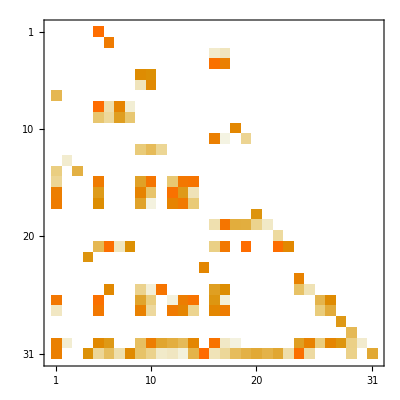

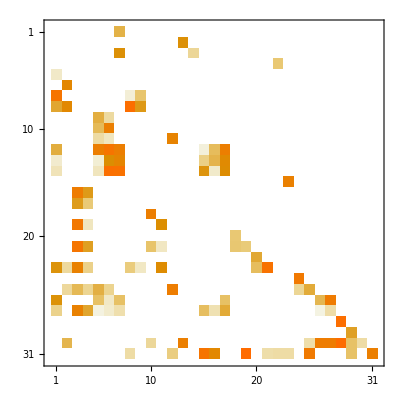

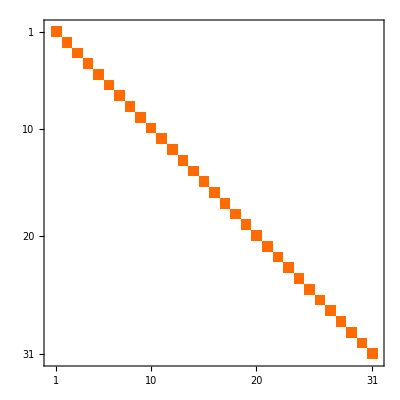

{}

```mathematica
reductionRules=GetReductionTableFromFile[FileNameJoin[{NotebookDirectory[],"KIRA/results/TTH/numerics_2147483647_0.m"}]];
PureIntegralN2=Expand[PureIntegralN/.reductionRules,Modulus->$P];
LaportaBasis=ReadList[FileNameJoin[{Directory[],"masters"}]];
LaportaBasis=Cases[LaportaBasis,_TTH,Infinity];
Basis=Cases[PureIntegralN2,_TTH,Infinity]//DeleteDuplicates;
NullInts=Thread[Rule[Complement[Basis,LaportaBasis],0]];
PureIntegralN2=PureIntegralN2/.NullInts;
BasisChangMat=Table[CoefficientArrays[Expand[PureIntegralN2/.epsrepl,Modulus->$P][[pos]],LaportaBasis],{pos,1,31}];
BasisChangMat=Normal[BasisChangMat[[All,2]]];
BasisChangMat//MatrixPlot
BasisChangMatInv=Inverse[BasisChangMat,Modulus->$P];
BasisChangMatInv//MatrixPlot
Expand[BasisChangMatInv.BasisChangMat,Modulus->$P]//MatrixPlot
```